```mathematica
<<MaTeX`
```

```mathematica
ConfigureMaTeX[
"pdfLaTeX"->"C:\\Program Files\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.02.0\\bin\\gswin64c.exe"
]
```

ConfigureMaTeX[pdfLaTeX→C:\Program Files\MiKTeX\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.02.0\bin\gswin64c.exe]

```mathematica
SetOptions[MaTeX,"FontSize"->16,"Magnification"->1.2];
```

SetOptions::optnf: FontSize is not a known option for MaTeX.

```mathematica
Solx0PFS[β0_,δ0_,δ1_]:=1-(δ0+δ1)/β0
```

```mathematica
Solve[Slopex0[x0,0,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]==0,x0]
```

{{x0→0},{x0→(β0-δ0-δ1)/β0}}

```mathematica
Slopex0[x0_,x1_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:= β0(1-x0-x1)x0+β0p*ϵ(1-x0-x1)x1-(δ0+δ1)x0-(δc+γ)x0*x1
```

```mathematica
Slopex1[x0_,x1_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:= β0p(1-ϵ)(1-x0-x1)x1-(δ0+δ1p)x1-(δc-γ)x0*x1
```

#### New David’s parametrization

```mathematica
Slopex0NEW[x0_,x1_,β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:= β0(1-x0-x1)x0+β1*ϵ(1-x0-x1)x1-(δ0+δ1)x0-(p0+χ)x0*x1
```

```mathematica
Slopex1NEW[x0_,x1_,β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:= β1(1-ϵ)(1-x0-x1)x1-(δ0+δ1g)x1-(p0-χ)x0*x1
```

```mathematica
Series[x1/.FullSimplify[Solve[{0==Slopex1NEW[x0,x1,β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]},{x1}]],{x0,0,1}]
```

{0,(δ0+δ1g+β1 (-1+ϵ))/(β1 (-1+ϵ))+((p0+β1-β1 ϵ-χ) x0)/(β1 (-1+ϵ))+O[x0]^2}

```mathematica
Series[Slopex0NEW[x0,(δ0+δ1g+β1 (-1+ϵ))/(β1 (-1+ϵ))+((p0+β1-β1 ϵ-χ) x0)/(β1 (-1+ϵ)),β0,β1,ϵ,δ0,δ1,δ1g,p0,χ],{x0,0,4}]
```

-((δ0+δ1g) ϵ (-β1+δ0+δ1g+β1 ϵ))/(β1 (-1+ϵ)^2)+(-δ0-δ1-(β0 (δ0+δ1g))/(β1 (-1+ϵ))-((δ0+δ1g+β1 (-1+ϵ)) (p0+χ))/(β1 (-1+ϵ))+β1 ϵ (((-δ0-δ1g) (p0+β1-β1 ϵ-χ))/(β1^2 (-1+ϵ)^2)+((δ0+δ1g+β1 (-1+ϵ)) (-p0+χ))/(β1^2 (-1+ϵ)^2))) x0+((β0 (-p0+χ))/(β1 (-1+ϵ))+(ϵ (p0+β1-β1 ϵ-χ) (-p0+χ))/(β1 (-1+ϵ)^2)-((p0+β1-β1 ϵ-χ) (p0+χ))/(β1 (-1+ϵ))) x0^2+O[x0]^5

```mathematica
Myccoeff[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=-((δ0+δ1g) ϵ (-β1+δ0+δ1g+β1 ϵ))/(β1 (-1+ϵ)^2)
```

```mathematica
Mybcoeff[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=(-δ0-δ1-(β0 (δ0+δ1g))/(β1 (-1+ϵ))-((δ0+δ1g+β1 (-1+ϵ)) (p0+χ))/(β1 (-1+ϵ))+β1 ϵ (((-δ0-δ1g) (p0+β1-β1 ϵ-χ))/(β1^2 (-1+ϵ)^2)+((δ0+δ1g+β1 (-1+ϵ)) (-p0+χ))/(β1^2 (-1+ϵ)^2)))
```

```mathematica
Myacoeff[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=((β0 (-p0+χ))/(β1 (-1+ϵ))+(ϵ (p0+β1-β1 ϵ-χ) (-p0+χ))/(β1 (-1+ϵ)^2)-((p0+β1-β1 ϵ-χ) (p0+χ))/(β1 (-1+ϵ)))
```

```mathematica
MySecondDegreeEquation[x0_,β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=Myccoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]+Mybcoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]*x0+Myacoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]*x0^2
```

```mathematica
FullSimplify[Myacoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]-acoeffB[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]]
```

0

#### Comparing with David’s solution

```mathematica
B0[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=β0-(δ0+δ1)
```

```mathematica
B1[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=β1*(1-ϵ)-(δ0+δ1g)
```

```mathematica
C0[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=β0+β1*ϵ+p0+χ
```

```mathematica
C1[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=β1*(1-ϵ)+p0-χ
```

```mathematica
acoeff[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=(1-(δ0+δ1g)/(β1(1-ϵ)))*(ϵ/(1-ϵ)*(δ0+δ1g)+χ+p0)-β0*(δ0+δ1g)/(β1(1-ϵ))
```

```mathematica
bcoeff[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=-(1+(p0-χ)/(β1(1-ϵ)))*(2*ϵ/(1-ϵ)*(δ0+δ1g)+χ+p0)-(δ0+δ1)-β0*(p0-χ)/(β1(1-ϵ))
```

```mathematica
ccoeff[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=ϵ/(1-ϵ)*(δ0+δ1g)*(1-(δ0+δ1g)/(β1(1-ϵ)))
```

```mathematica
acoeffB[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=(C0[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]*C1[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ])/(β1*(1-ϵ))-(β1*ϵ)*(C1[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]/(β1*(1-ϵ)))^2-β0
```

```mathematica
bcoeffB[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=B0[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]-ϵ/(1-ϵ)C1[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]+2β1*ϵ*(1/(β1*(1-ϵ)))^2*B1[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]*C1[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]-(C0[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]*B1[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ])/(β1*(1-ϵ))
```

```mathematica
ccoeffB[β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=β1*ϵ*(B1[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]/(β1*(1-ϵ))*(1-B1[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]/(β1*(1-ϵ))))
```

```mathematica
DavidSecondDegreeEq[x0_,β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=ccoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]+bcoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]*x0+acoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]*x0^2
```

```mathematica
DavidSecondDegreeEqB[x0_,β0_,β1_,ϵ_,δ0_,δ1_,δ1g_,p0_,χ_]:=ccoeffB[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]+bcoeffB[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]*x0+acoeffB[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]*x0^2
```

```mathematica
FullSimplify[DavidSecondDegreeEq[x0,β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]-DavidSecondDegreeEqB[x0,β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]]
```

-(x0 (p0+δ0+δ1g-χ) (β0+p0 (1+x0-ϵ-2 x0 ϵ)+χ-ϵ (β0+β1 (-1+ϵ)+χ)+x0 (β0-β0 ϵ+(δ0+δ1g+β1 (-1+ϵ)) ϵ+χ)))/(β1 (-1+ϵ)^2)

```mathematica
FullSimplify[DavidSecondDegreeEq[x0,β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]-MySecondDegreeEquation[x0,β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]]
```

-(x0 (p0+δ0+δ1g-χ) (β0+p0 (1+x0-ϵ-2 x0 ϵ)+χ-ϵ (β0+β1 (-1+ϵ)+χ)+x0 (β0-β0 ϵ+(δ0+δ1g+β1 (-1+ϵ)) ϵ+χ)))/(β1 (-1+ϵ)^2)

```mathematica
FullSimplify[acoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]-Myacoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]]
```

-((p0+δ0+δ1g-χ) (p0+β0-2 p0 ϵ+(-β0+δ0+δ1g+β1 (-1+ϵ)) ϵ+χ))/(β1 (-1+ϵ)^2)

```mathematica
FullSimplify[bcoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]-Mybcoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]]
```

((p0+δ0+δ1g-χ) (p0+β0+β1 ϵ+χ))/(β1 (-1+ϵ))

```mathematica
FullSimplify[ccoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]-Myccoeff[β0,β1,ϵ,δ0,δ1,δ1g,p0,χ]]
```

0

#### Old stuff from January 2025

```mathematica
SteadySols[β0_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:= NSolve[{0==Slopex0[x0,x1,β0,0.,β0p,ϵ,γ,δ0,δ1,δ1p,δc],0==Slopex1[x0,x1,β0,0.,β0p,ϵ,γ,δ0,δ1,δ1p,δc],x0>=0,x1>=0},{x0,x1}]
```

```mathematica
Sols[x00_,x10_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:= NDSolve[{x0'[τ]==Slopex0[x0[τ],x1[τ],β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc],x1'[τ]==Slopex1[x0[τ],x1[τ],β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc],x0[0]==x00,x1[0]==x10},{x0,x1},{τ,0,100}]
```

```mathematica
Sols[0.1,0.1,ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]
```

{{x0→InterpolatingFunction[…],x1→InterpolatingFunction[…]}}

```mathematica
Solve[{Slopex0[x0,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]==0,Slopex1[x0,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]==0 },{x0,x1}];
```

```mathematica
Solve[{Slopex1[x0,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]==0 },{x1}]
```

{{x1→0},{x1→(-β0p+x0 β0p-x0 γ+δ0+δ1p+x0 δc+β0p ϵ-x0 β0p ϵ)/(β0p (-1+ϵ))}}

```mathematica
FullSimplify[Slopex0[x0,(-β0p+x0 β0p-x0 γ+δ0+δ1p+x0 δc+β0p ϵ-x0 β0p ϵ)/(β0p (-1+ϵ)),β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]]
```

1/(β0p (-1+ϵ)^2)(-((δ0+δ1p) (δ0+δ1p+β0p (-1+ϵ)) ϵ)+x0^2 (β0 (γ-δc) (-1+ϵ)-(γ-δc+β0p (-1+ϵ)) (γ+δc-2 δc ϵ))+x0 ((δ0+δ1p) (β0+γ+δc-β0 ϵ+γ ϵ-3 δc ϵ)+β0p (-1+ϵ) (γ+δ0+δ1+δc-δ1 ϵ+δ1p ϵ-2 δc ϵ)))

```mathematica
FullSimplify[Series[Slopex0[x0,(-β0p+x0 β0p-x0 γ+δ0+δ1p+x0 δc+β0p ϵ-x0 β0p ϵ)/(β0p (-1+ϵ)),β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc],{x0,0,2}]]
```

-((δ0+δ1p) (δ0+δ1p+β0p (-1+ϵ)) ϵ)/(β0p (-1+ϵ)^2)+(((δ0+δ1p) (β0+γ+δc-β0 ϵ+γ ϵ-3 δc ϵ)+β0p (-1+ϵ) (γ+δ0+δ1+δc-δ1 ϵ+δ1p ϵ-2 δc ϵ)) x0)/(β0p (-1+ϵ)^2)+((β0 (γ-δc) (-1+ϵ)-(γ-δc+β0p (-1+ϵ)) (γ+δc-2 δc ϵ)) x0^2)/(β0p (-1+ϵ)^2)+O[x0]^3

```mathematica
C0[β0_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:=-((δ0+δ1p) (δ0+δ1p+β0p (-1+ϵ)) ϵ)/(β0p (-1+ϵ)^2)
```

```mathematica
B0[β0_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:=((δ0+δ1p) (β0+γ+δc-β0 ϵ+γ ϵ-3 δc ϵ)+β0p (-1+ϵ) (γ+δ0+δ1+δc-δ1 ϵ+δ1p ϵ-2 δc ϵ))/(β0p (-1+ϵ)^2)
```

```mathematica
A0[β0_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:=(β0 (γ-δc) (-1+ϵ)-(γ-δc+β0p (-1+ϵ)) (γ+δc-2 δc ϵ))/(β0p (-1+ϵ)^2)
```

```mathematica
Polynomialx1[x0_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:= A0[β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]*x0^2+ B0[β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]*x0+ C0[β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]
```

```mathematica
Discriminant2Sols[β0_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:=  B0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc]^2-4*A0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc]* C0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc]
```

```mathematica
SolDoublex1[x0_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:= (-β0p+x0 β0p-x0 γ+δ0+δ1p+x0 δc+β0p ϵ-x0 β0p ϵ)/(β0p (-1+ϵ))
```

```mathematica
FullSimplify[SolDoublex1[x0,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]]
```

1-x0+(δ0+δ1p+x0 (-γ+δc))/(β0p (-1+ϵ))

```mathematica
B0[β0,β0*(1-c),0,γ,δ0,δ1,δ1*(1-r),δc]
```

((δ0+(1-r) δ1) (β0+γ+δc)-(1-c) β0 (γ+δ0+δ1+δc))/((1-c) β0)

```mathematica
A0[β0,β0*(1-c),0,γ,δ0,δ1,δ1*(1-r),δc]
```

(-β0 (γ-δc)-(-((1-c) β0)+γ-δc) (γ+δc))/((1-c) β0)

```mathematica
SolDoublex0A[β0_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:= (- B0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc]-Sqrt[ B0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc]^2-4* A0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc]* C0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc]])/(2*A0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc])
```

```mathematica
SolDoublex0B[β0_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:= (- B0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc]+Sqrt[ B0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc]^2-4* A0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc]* C0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc]])/(2*A0[β0,β0p,ϵ,γ,δ0,δ1,δ1p,δc])
```

```mathematica
FullSimplify[Discriminant2Sols[β0,β0*(1-c),ϵ,γ,δ0,δ1,δ1*(1-r),δc]]
```

1/((β0-c β0)^2 (-1+ϵ)^4)(((δ0+δ1-r δ1) (β0+γ+δc-β0 ϵ+γ ϵ-3 δc ϵ)-(-1+c) β0 (-1+ϵ) (γ+δ0+δ1+δc-r δ1 ϵ-2 δc ϵ))^2+4 (δ0+δ1-r δ1) ϵ (δ0+δ1-r δ1+β0 (-1+c+ϵ-c ϵ)) (β0 (γ-δc) (-1+ϵ)-(γ+δc-2 δc ϵ) (γ-δc+β0 (-1+c+ϵ-c ϵ))))

```mathematica
Isoβ0A[β0_,ϵ_,γ_,δ0_,δ1_,δc_,c_,r_]:=(-2 √(-((-1+c) (δ0+δ1-r δ1)^2 (-γ (γ+r δ1)+2 δ0 δc-(-2+r) δ1 δc+δc^2) (-1+ϵ)^4 ϵ ((-r δ1+c (δ0+δ1)) (γ+δc)-2 (-1+c) (δ0+δ1) δc ϵ)))+(δ0+δ1-r δ1) (-1+ϵ)^2 (-((γ+δc) ((-1+c) γ-r δ1-δc+c (δ0+δ1+δc)))+(-1+c) (-r δ1 (γ+δc)+2 δc (γ+2 (δ0+δ1)+δc)) ϵ))/((-1+ϵ)^2 ((γ-c γ+r δ1+δc-c (δ0+δ1+δc))^2-2 (-1+c) (2 c γ δ0+2 c γ δ1-r γ δ1-c r γ δ1+c r δ0 δ1+c r δ1^2-r^2 δ1^2+(-1+c) (2 γ+4 δ0-(-4+r) δ1) δc+2 (-1+c) δc^2) ϵ+(-1+c)^2 (r^2 δ1^2-4 r δ1 δc+4 δc (2 (δ0+δ1)+δc)) ϵ^2))
```

```mathematica
Isoβ0B[β0_,ϵ_,γ_,δ0_,δ1_,δc_,c_,r_]:=(2 √(-((-1+c) (δ0+δ1-r δ1)^2 (-γ (γ+r δ1)+2 δ0 δc-(-2+r) δ1 δc+δc^2) (-1+ϵ)^4 ϵ ((-r δ1+c (δ0+δ1)) (γ+δc)-2 (-1+c) (δ0+δ1) δc ϵ)))+(δ0+δ1-r δ1) (-1+ϵ)^2 (-((γ+δc) ((-1+c) γ-r δ1-δc+c (δ0+δ1+δc)))+(-1+c) (-r δ1 (γ+δc)+2 δc (γ+2 (δ0+δ1)+δc)) ϵ))/((-1+ϵ)^2 ((γ-c γ+r δ1+δc-c (δ0+δ1+δc))^2-2 (-1+c) (2 c γ δ0+2 c γ δ1-r γ δ1-c r γ δ1+c r δ0 δ1+c r δ1^2-r^2 δ1^2+(-1+c) (2 γ+4 δ0-(-4+r) δ1) δc+2 (-1+c) δc^2) ϵ+(-1+c)^2 (r^2 δ1^2-4 r δ1 δc+4 δc (2 (δ0+δ1)+δc)) ϵ^2))
```

```mathematica
FullSimplify[Solve[(((δ0+δ1-r δ1) (β0+γ+δc-β0 ϵ+γ ϵ-3 δc ϵ)-(-1+c) β0 (-1+ϵ) (γ+δ0+δ1+δc-r δ1 ϵ-2 δc ϵ))^2+4 (δ0+δ1-r δ1) ϵ (δ0+δ1-r δ1+β0 (-1+c+ϵ-c ϵ)) (β0 (γ-δc) (-1+ϵ)-(γ+δc-2 δc ϵ) (γ-δc+β0 (-1+c+ϵ-c ϵ))))==0,β0]]
```

{{β0→(-2 √(-((-1+c) (δ0+δ1-r δ1)^2 (-γ (γ+r δ1)+2 δ0 δc-(-2+r) δ1 δc+δc^2) (-1+ϵ)^4 ϵ ((-r δ1+c (δ0+δ1)) (γ+δc)-2 (-1+c) (δ0+δ1) δc ϵ)))+(δ0+δ1-r δ1) (-1+ϵ)^2 (-((γ+δc) ((-1+c) γ-r δ1-δc+c (δ0+δ1+δc)))+(-1+c) (-r δ1 (γ+δc)+2 δc (γ+2 (δ0+δ1)+δc)) ϵ))/((-1+ϵ)^2 ((γ-c γ+r δ1+δc-c (δ0+δ1+δc))^2-2 (-1+c) (2 c γ δ0+2 c γ δ1-r γ δ1-c r γ δ1+c r δ0 δ1+c r δ1^2-r^2 δ1^2+(-1+c) (2 γ+4 δ0-(-4+r) δ1) δc+2 (-1+c) δc^2) ϵ+(-1+c)^2 (r^2 δ1^2-4 r δ1 δc+4 δc (2 (δ0+δ1)+δc)) ϵ^2))},{β0→(2 √(-((-1+c) (δ0+δ1-r δ1)^2 (-γ (γ+r δ1)+2 δ0 δc-(-2+r) δ1 δc+δc^2) (-1+ϵ)^4 ϵ ((-r δ1+c (δ0+δ1)) (γ+δc)-2 (-1+c) (δ0+δ1) δc ϵ)))+(δ0+δ1-r δ1) (-1+ϵ)^2 (-((γ+δc) ((-1+c) γ-r δ1-δc+c (δ0+δ1+δc)))+(-1+c) (-r δ1 (γ+δc)+2 δc (γ+2 (δ0+δ1)+δc)) ϵ))/((-1+ϵ)^2 ((γ-c γ+r δ1+δc-c (δ0+δ1+δc))^2-2 (-1+c) (2 c γ δ0+2 c γ δ1-r γ δ1-c r γ δ1+c r δ0 δ1+c r δ1^2-r^2 δ1^2+(-1+c) (2 γ+4 δ0-(-4+r) δ1) δc+2 (-1+c) δc^2) ϵ+(-1+c)^2 (r^2 δ1^2-4 r δ1 δc+4 δc (2 (δ0+δ1)+δc)) ϵ^2))}}

```mathematica
Jx0[x0_,x1_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:=D[{Slopex0[x,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc],Slopex1[x,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc] },{x}]/.x->x0
```

```mathematica
Jx1[x0_,x1_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:=D[{Slopex0[x0,x,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc],Slopex1[x0,x,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc] },x]/.x->x1
```

```mathematica
Jx1[x0,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc][[1]]
```

-x0 β0-x0 (γ+δc)+(1-x0-x1) β0p ϵ-x1 β0p ϵ

```mathematica
JacDynamics[x0_,x1_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:={{-x0 β0+(1-x0-x1) β0-δ0-δ1-x1 (γ+δc)-x1 β0p ϵ,-x0 β0-x0 (γ+δc)+(1-x0-x1) β0p ϵ-x1 β0p ϵ},{-x1 (-γ+δc)-x1 β0p (1-ϵ),-δ0-δ1p-x0 (-γ+δc)+(1-x0-x1) β0p (1-ϵ)-x1 β0p (1-ϵ)}}
```

```mathematica
JacDynamics2[x0_,x1_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:={{Jx0[x0,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc][[1]],Jx1[x0,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc][[1]]},{Jx0[x0,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc][[2]],Jx1[x0,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc][[2]]}}
```

```mathematica
FullSimplify[Det[JacDynamics[(β0-δ0-δ1)/β0,0,β0,β1,β0*(1-c),ϵ,γ,δ0,δ1,δ1*(1-r),δc]]-Det[JacDynamics2[(β0-δ0-δ1)/β0,0,β0,β1,β0*(1-c),ϵ,γ,δ0,δ1,δ1*(1-r),δc]]]
```

0

```mathematica
FullSimplify[JacDynamics2[x0,0,β0,β1,β0*(1-c),ϵ,γ,δ0,δ1,δ1*(1-r),δc]]
```

{{β0-δ0-δ1,-((-1+c) β0 ϵ)},{0,-δ0+(-1+r) δ1+(-1+c) β0 (-1+ϵ)}}

```mathematica
FullSimplify[Tr[JacDynamics2[x0,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]]]
```

-((-1+2 x0+x1) β0)+β0p-2 δ0-δ1-δ1p-x1 (2 β0p+γ+δc)+x0 (γ-δc+β0p (-1+ϵ))+(-1+x1) β0p ϵ

```mathematica
DetEigenvalues[x0_,x1_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:=β0 ((-1+x1) (δ0+δ1p)+x0 (γ+2 (δ0+δ1p)-δc)+2 x0^2 (-γ+δc)-(-1+x0+x1) (-1+2 x0+2 x1) β0p (-1+ϵ))+2 x1^2 β0p (γ+δc-2 δc ϵ)+(δ0+δ1) (δ0+δ1p+x0 (-γ+δc)+β0p (-1+x0+ϵ-x0 ϵ))+x1 ((δ0+δ1p) (γ+δc)-β0p (γ+δc+δ0 (-2+ϵ)+2 δ1 (-1+ϵ)-(δ1p+2 δc) ϵ))
```

```mathematica
TraceEigenvalues[x0_,x1_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:=-((-1+2 x0+x1) β0)+β0p-2 δ0-δ1-δ1p-x1 (2 β0p+γ+δc)+x0 (γ-δc+β0p (-1+ϵ))+(-1+x1) β0p ϵ
```

```mathematica
DiscriminantEigenvalues[x0_,x1_,β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]:= TraceEigenvalues[x0,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]^2-4*DetEigenvalues[x0,x1,β0,β1,β0p,ϵ,γ,δ0,δ1,δ1p,δc]
```

```mathematica
λ2[β0_,ϵ_,γ_,δ0_,δ1_,δc_,c_,r_]:=γ+r δ1-c (δ0+δ1)-((δ0+δ1) (γ-δc))/β0-δc+(-1+c) (δ0+δ1) ϵ
```

```mathematica
Condx1[x0_,β0_,ϵ_,γ_,δ0_,δ1_,δc_,c_,r_]:= 1-x0-1/((1-c)*(1-r))*(1-(β0-δ0-δ1)/β0+1/β0*(x0*(γ-δc)+r*δ1))
```

```mathematica
FullSimplify[JacDynamics2[0,0,β0,β1,β0*(1-c),ϵ,γ,δ0,δ1,δ1*(1-r),δc]]
```

{{β0-δ0-δ1,-((-1+c) β0 ϵ)},{0,-δ0+(-1+r) δ1+(-1+c) β0 (-1+ϵ)}}

```mathematica
Eigenvalues[JacDynamics2[x0,x1,β0,β1,β0*(1-c),ϵ,γ,δ0,δ0,δ0*(1-r),δc]]
```

{1/2 (2 β0-c β0-3 x0 β0+c x0 β0-3 x1 β0+2 c x1 β0+x0 γ-x1 γ-4 δ0+r δ0-x0 δc-x1 δc-β0 ϵ+c β0 ϵ+x0 β0 ϵ-c x0 β0 ϵ+x1 β0 ϵ-c x1 β0 ϵ-√((-2 β0+c β0+3 x0 β0-c x0 β0+3 x1 β0-2 c x1 β0-x0 γ+x1 γ+4 δ0-r δ0+x0 δc+x1 δc+β0 ϵ-c β0 ϵ-x0 β0 ϵ+c x0 β0 ϵ-x1 β0 ϵ+c x1 β0 ϵ)^2-4 (β0^2-c β0^2-3 x0 β0^2+3 c x0 β0^2+2 x0^2 β0^2-2 c x0^2 β0^2-3 x1 β0^2+3 c x1 β0^2+4 x0 x1 β0^2-4 c x0 x1 β0^2+2 x1^2 β0^2-2 c x1^2 β0^2+x0 β0 γ-2 x0^2 β0 γ-x1 β0 γ+c x1 β0 γ+2 x1^2 β0 γ-2 c x1^2 β0 γ-4 β0 δ0+2 c β0 δ0+r β0 δ0+6 x0 β0 δ0-2 c x0 β0 δ0-2 r x0 β0 δ0+6 x1 β0 δ0-4 c x1 β0 δ0-r x1 β0 δ0-2 x0 γ δ0+2 x1 γ δ0-r x1 γ δ0+4 δ0^2-2 r δ0^2-x0 β0 δc+2 x0^2 β0 δc-x1 β0 δc+c x1 β0 δc+2 x1^2 β0 δc-2 c x1^2 β0 δc+2 x0 δ0 δc+2 x1 δ0 δc-r x1 δ0 δc-β0^2 ϵ+c β0^2 ϵ+3 x0 β0^2 ϵ-3 c x0 β0^2 ϵ-2 x0^2 β0^2 ϵ+2 c x0^2 β0^2 ϵ+3 x1 β0^2 ϵ-3 c x1 β0^2 ϵ-4 x0 x1 β0^2 ϵ+4 c x0 x1 β0^2 ϵ-2 x1^2 β0^2 ϵ+2 c x1^2 β0^2 ϵ+2 β0 δ0 ϵ-2 c β0 δ0 ϵ-2 x0 β0 δ0 ϵ+2 c x0 β0 δ0 ϵ-2 x1 β0 δ0 ϵ+2 c x1 β0 δ0 ϵ-r x1 β0 δ0 ϵ+c r x1 β0 δ0 ϵ+2 x1 β0 δc ϵ-2 c x1 β0 δc ϵ-4 x1^2 β0 δc ϵ+4 c x1^2 β0 δc ϵ))),1/2 (2 β0-c β0-3 x0 β0+c x0 β0-3 x1 β0+2 c x1 β0+x0 γ-x1 γ-4 δ0+r δ0-x0 δc-x1 δc-β0 ϵ+c β0 ϵ+x0 β0 ϵ-c x0 β0 ϵ+x1 β0 ϵ-c x1 β0 ϵ+√((-2 β0+c β0+3 x0 β0-c x0 β0+3 x1 β0-2 c x1 β0-x0 γ+x1 γ+4 δ0-r δ0+x0 δc+x1 δc+β0 ϵ-c β0 ϵ-x0 β0 ϵ+c x0 β0 ϵ-x1 β0 ϵ+c x1 β0 ϵ)^2-4 (β0^2-c β0^2-3 x0 β0^2+3 c x0 β0^2+2 x0^2 β0^2-2 c x0^2 β0^2-3 x1 β0^2+3 c x1 β0^2+4 x0 x1 β0^2-4 c x0 x1 β0^2+2 x1^2 β0^2-2 c x1^2 β0^2+x0 β0 γ-2 x0^2 β0 γ-x1 β0 γ+c x1 β0 γ+2 x1^2 β0 γ-2 c x1^2 β0 γ-4 β0 δ0+2 c β0 δ0+r β0 δ0+6 x0 β0 δ0-2 c x0 β0 δ0-2 r x0 β0 δ0+6 x1 β0 δ0-4 c x1 β0 δ0-r x1 β0 δ0-2 x0 γ δ0+2 x1 γ δ0-r x1 γ δ0+4 δ0^2-2 r δ0^2-x0 β0 δc+2 x0^2 β0 δc-x1 β0 δc+c x1 β0 δc+2 x1^2 β0 δc-2 c x1^2 β0 δc+2 x0 δ0 δc+2 x1 δ0 δc-r x1 δ0 δc-β0^2 ϵ+c β0^2 ϵ+3 x0 β0^2 ϵ-3 c x0 β0^2 ϵ-2 x0^2 β0^2 ϵ+2 c x0^2 β0^2 ϵ+3 x1 β0^2 ϵ-3 c x1 β0^2 ϵ-4 x0 x1 β0^2 ϵ+4 c x0 x1 β0^2 ϵ-2 x1^2 β0^2 ϵ+2 c x1^2 β0^2 ϵ+2 β0 δ0 ϵ-2 c β0 δ0 ϵ-2 x0 β0 δ0 ϵ+2 c x0 β0 δ0 ϵ-2 x1 β0 δ0 ϵ+2 c x1 β0 δ0 ϵ-r x1 β0 δ0 ϵ+c r x1 β0 δ0 ϵ+2 x1 β0 δc ϵ-2 c x1 β0 δc ϵ-4 x1^2 β0 δc ϵ+4 c x1^2 β0 δc ϵ)))}

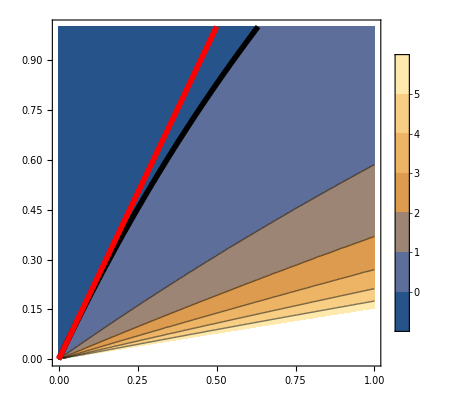

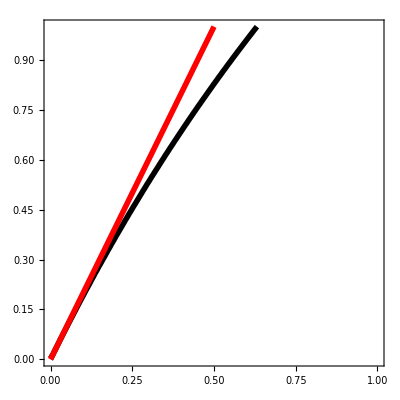

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;δδc=1.5;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==2*δδ0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red}]]
Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==2*δδ0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red}]]
```

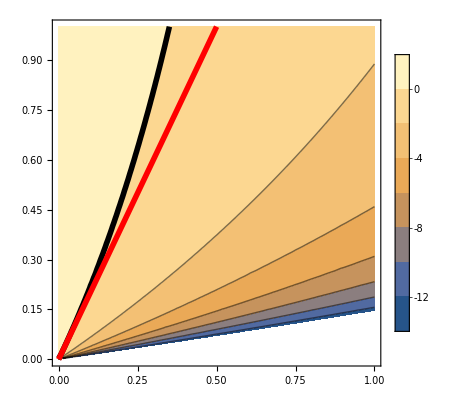

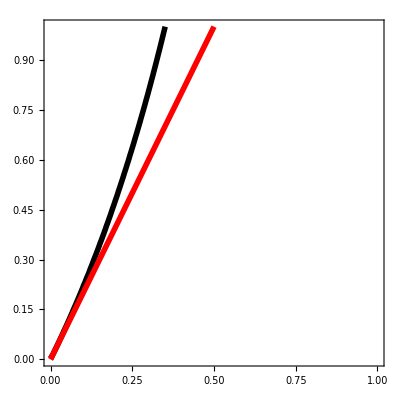

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;δδc=0.05;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==2*δδ0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red}]]
Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==2*δδ0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red}]]
```

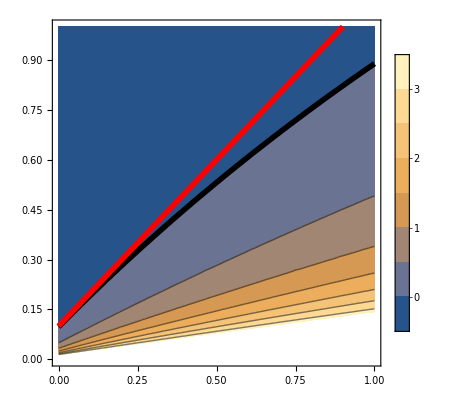

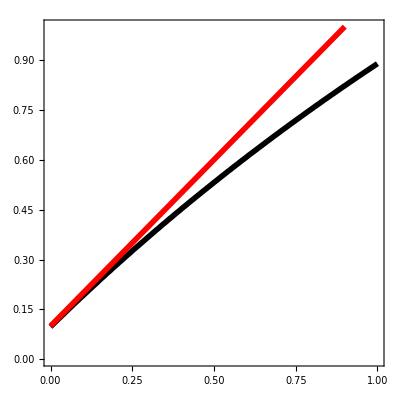

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=1.5;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ1,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red}]]
Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ1,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red}]]
```

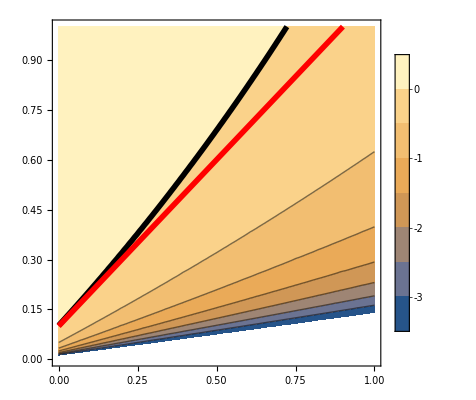

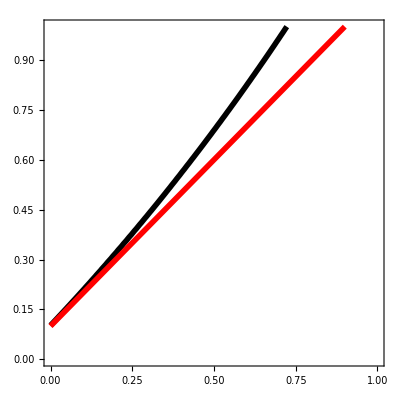

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.5;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ1,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red}]]
Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ1,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red}]]
```

```mathematica
Discriminant2Sols[β0_,β1_,β0p_,ϵ_,γ_,δ0_,δ1_,δ1p_,δc_]
```

```mathematica
Isoβ0B[0.5,ϵϵ,γγ,0.5,0.5,δδc,cc,rr]
```

1.39374

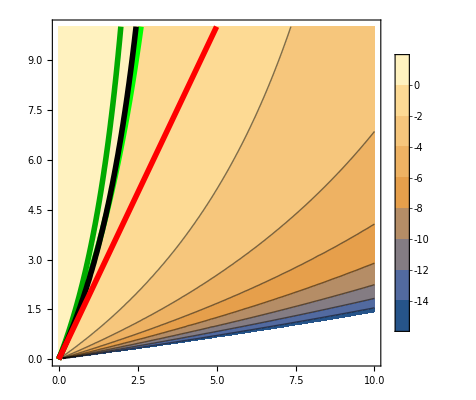

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.0;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,10},{ββ0,0,10},PlotLegends->Automatic],ContourPlot[ββ0==Isoβ0A[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,3},{ββ0,0,10},ContourStyle->{Thickness[0.01],Green}],ContourPlot[ββ0==Isoβ0B[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,3},{ββ0,0,10},ContourStyle->{Thickness[0.01],Darker[Green]}],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ0,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

```mathematica
Ç
```

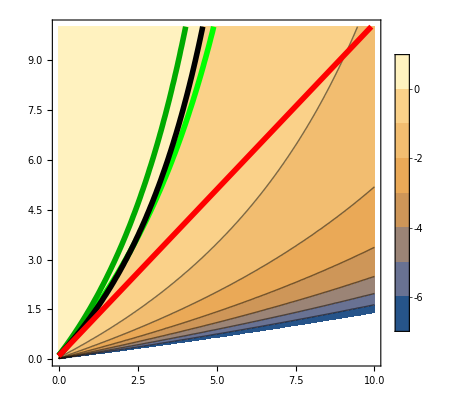

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr],{δδ0,0,10},{ββ0,0,10},PlotLegends->Automatic],ContourPlot[ββ0==Isoβ0A[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr],{δδ0,0,7},{ββ0,0,10},ContourStyle->{Thickness[0.01],Green}],ContourPlot[ββ0==Isoβ0B[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr],{δδ0,0,7},{ββ0,0,10},ContourStyle->{Thickness[0.01],Darker[Green]}],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr]==0,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ1,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

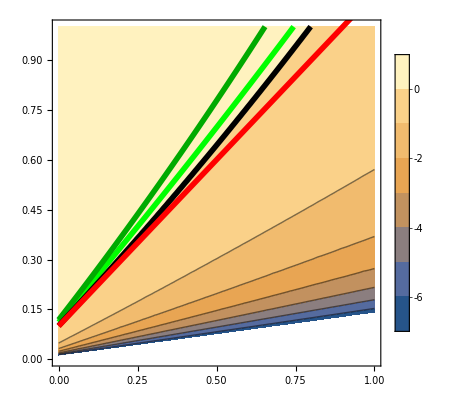

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[ββ0==Isoβ0A[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Green}],ContourPlot[ββ0==Isoβ0B[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Green]}],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ1,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

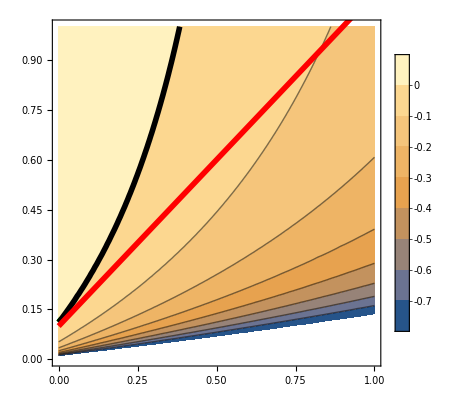

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.9;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[ββ0==Isoβ0A[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Green}],ContourPlot[ββ0==Isoβ0B[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Green]}],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ1,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

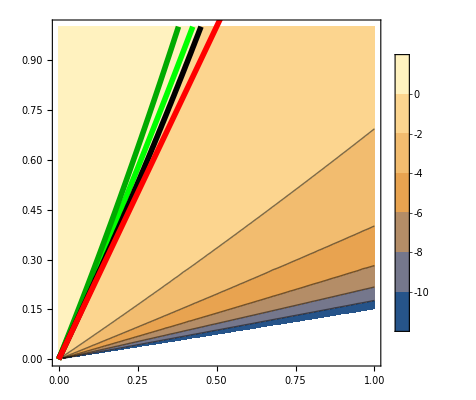

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[ββ0==Isoβ0A[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Green}],ContourPlot[ββ0==Isoβ0B[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Green]}],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ0,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

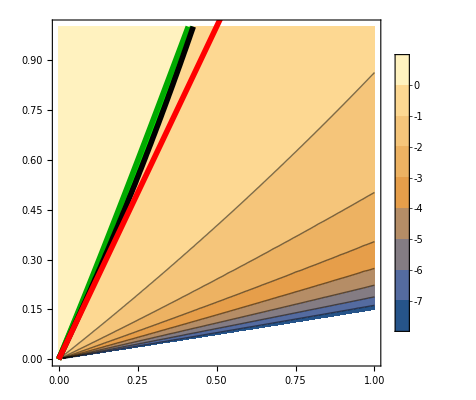

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.4;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[ββ0==Isoβ0A[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Green}],ContourPlot[ββ0==Isoβ0B[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Green]}],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ0,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

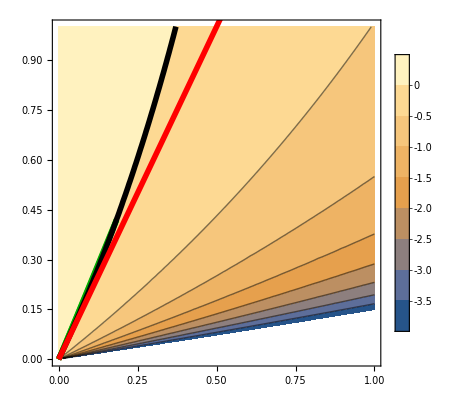

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.7;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[ββ0==Isoβ0A[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Green}],ContourPlot[ββ0==Isoβ0B[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Green]}],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ0,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

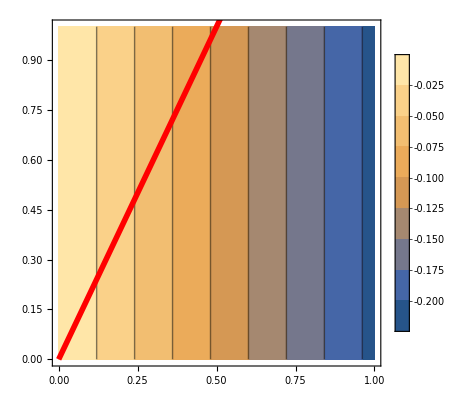

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=1;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[ββ0==Isoβ0A[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Green}],ContourPlot[ββ0==Isoβ0B[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Green]}],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ0,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

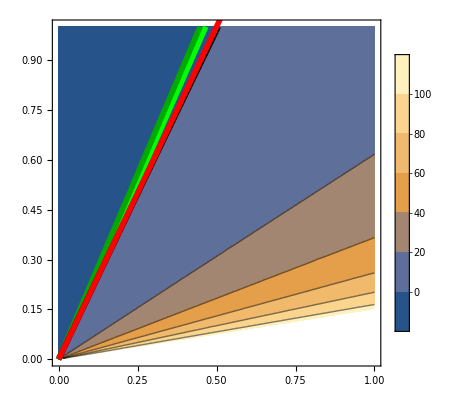

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=10;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[ββ0==Isoβ0A[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Green}],ContourPlot[ββ0==Isoβ0B[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Green]}],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ0,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

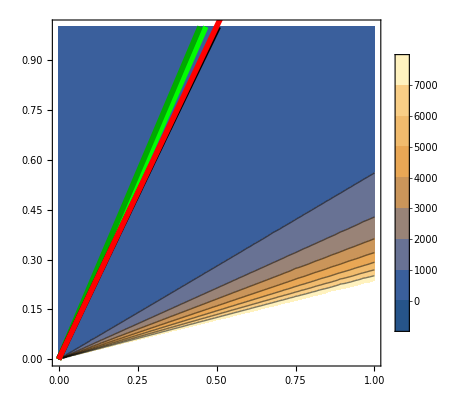

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=10;Show[ContourPlot[Discriminant2Sols[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[ββ0==Isoβ0A[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Green}],ContourPlot[ββ0==Isoβ0B[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Green]}],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ0,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

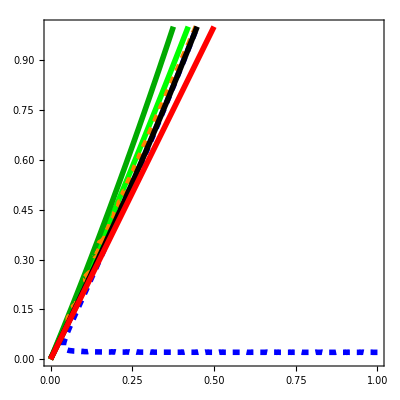

```mathematica
rr=0.0;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[ββ0==Isoβ0A[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Green}],ContourPlot[ββ0==Isoβ0B[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr],{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Green]}],ContourPlot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic],ContourPlot[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Orange,Dashed},PlotLegends->Automatic],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red}]]
```

#### Stability of x0,x1 >0

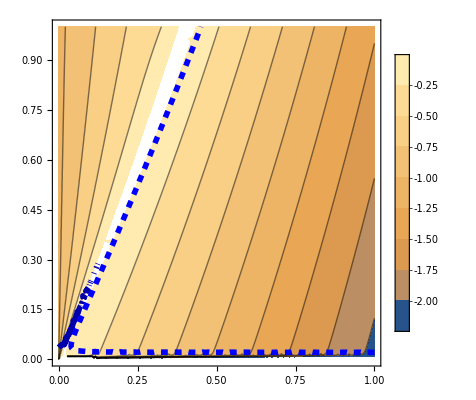

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[Eigenvalues[JacDynamics2[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]][[1]],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue]}],ContourPlot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic]]
```

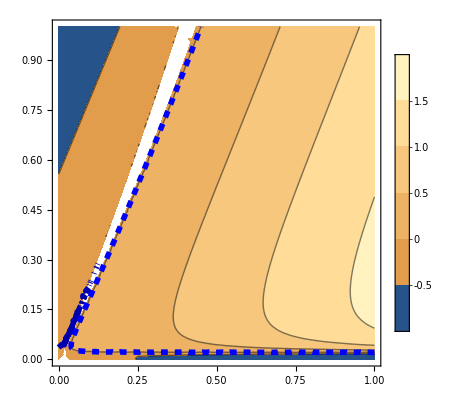

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[Eigenvalues[JacDynamics2[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]][[2]],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue]}],ContourPlot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic]]
```

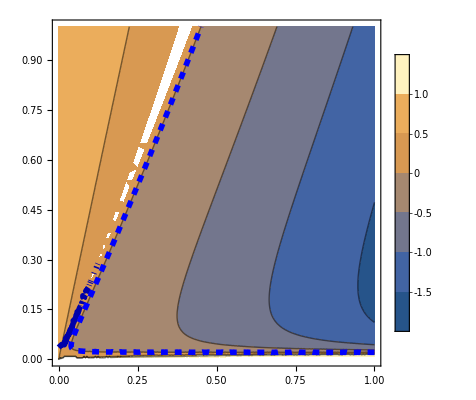

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue]}],ContourPlot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic]]
```

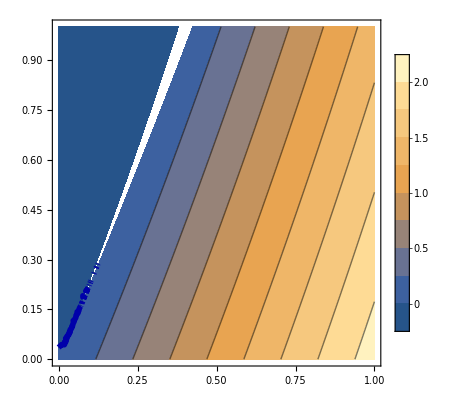

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue]}]]
```

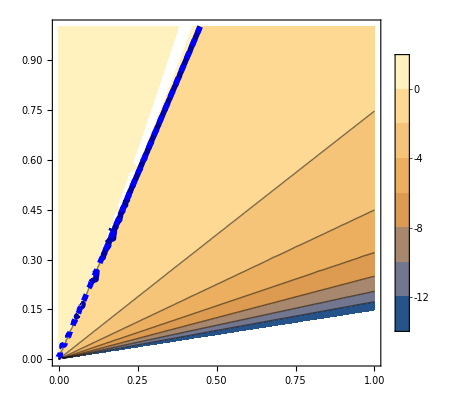

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue]}],ContourPlot[SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic]]
```

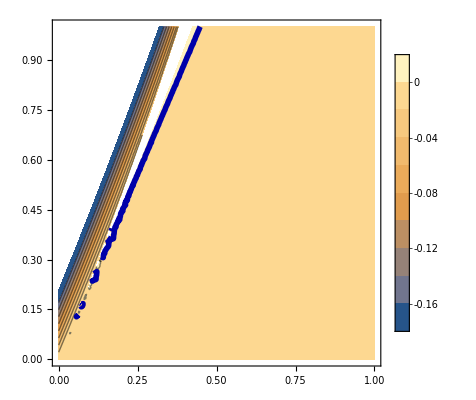

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue]}]]
```

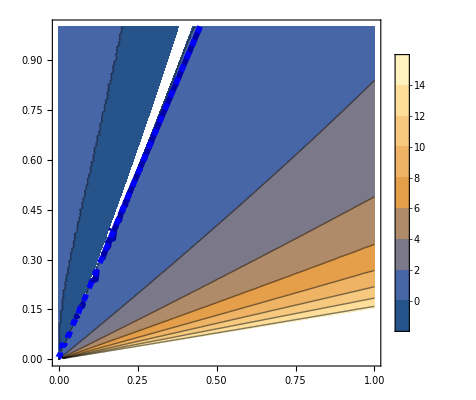

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[Eigenvalues[JacDynamics2[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]][[1]],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue]}],ContourPlot[SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic]]
```

```mathematica
Condx1[]
```

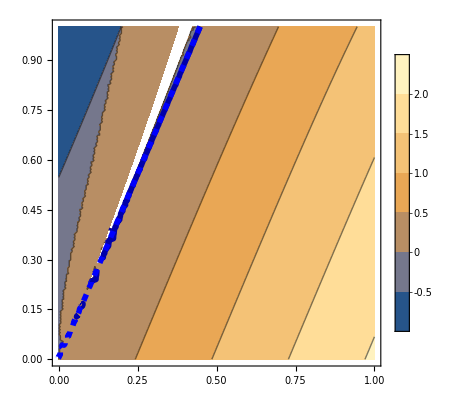

```mathematica
rr=0.01;ϵϵ=0.01;cc=0.1;γγ=1;
δδ1=0.1;δδc=0.05;Show[ContourPlot[Eigenvalues[JacDynamics2[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]][[2]],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue]}],ContourPlot[SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic]]
```

#### Stability of x0=x1=0 and x0>0,x1=0 and x1>0,x2>0 (with δ1=δ0)

```mathematica
texStyle={FontFamily-> "Palatino Linotype",FontSize->14};
```

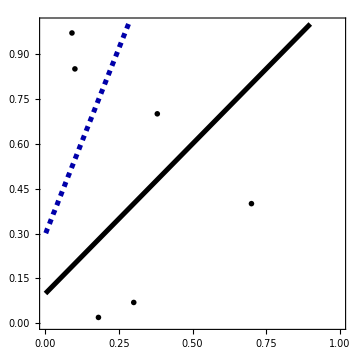

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;δδ1=0.1;
δδc=3;Show[ContourPlot[Condx1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ1,δδ1*(1-rr),δδc],ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue],Dashing[0.01,0.02]}],ContourPlot[ββ0==(δδ0+δδ1),{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black},PlotLegends->Automatic],Graphics[Text[Style[MaTeX@"\\boxed{\\gamma<\\delta_c}"],{0.09,0.97}]],Graphics[Text[Style[MaTeX["\\text{PFS=Plasmid-free solution}",FontSize->12]],{0.3,0.07}]],Graphics[Text[Style[MaTeX["\\text{C=Coexistence}",FontSize->12]],{0.18,0.02}]],Graphics[Text[Style[MaTeX@"\\text{Extinction}"],{0.7,0.4}]],Graphics[Text[Style[MaTeX@"\\text{PFS}"],{0.38,0.7}]],Graphics[Text[Style[MaTeX@"\\text{C+PFS}"],{0.1,0.85}]],ImageSize->Medium,Frame->True,BaseStyle->texStyle,FrameLabel->MaTeX@{"\\delta_0 \, \\text{(basal mortality)}","\\beta_0 \, \\text{(cell division rate)}"}]
```

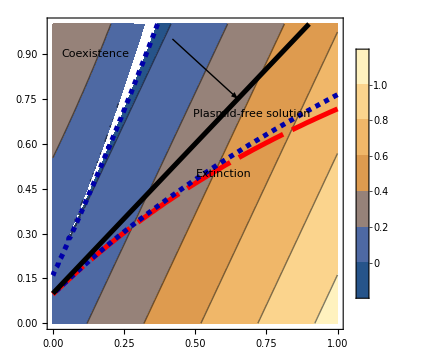

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;
δδc=2;Show[ContourPlot[Eigenvalues[JacDynamics2[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ1,δδ1*(1-rr),δδc],SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ1,δδ1*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ1,δδ1*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ1,δδ1*(1-rr),δδc]][[2]],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red,Dashing[{0.1,0.02}]}],ContourPlot[DiscriminantEigenvalues[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ1,δδ1*(1-rr),δδc],SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ1,δδ1*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ1,δδ1*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ1,δδ1*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue],Dashing[0.01,0.02]}],ContourPlot[ββ0==(δδ0+δδ1),{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black},PlotLegends->Automatic],Graphics[Text[Style["Extinction"],{0.6,0.5}]],Graphics[Arrow[{{0.42,0.95},{0.65,0.75}}]],Graphics[Text[Style["Plasmid-free solution"],{0.7,0.7}]],Graphics[Text[Style["Coexistence"],{0.15,0.9}]],ImageSize->Medium,Frame->True,BaseStyle->texStyle,FrameLabel->MaTeX@{"\\delta_0","\\beta_0"}]
```

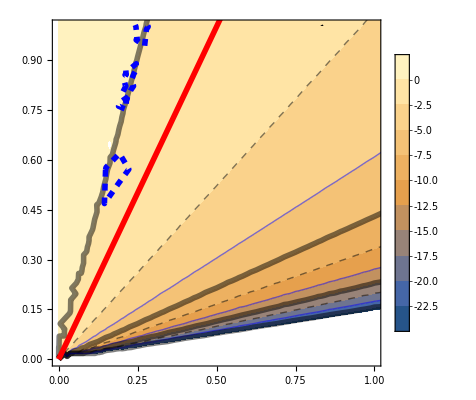

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;
δδc=2;Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,4},{ββ0,0,4},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic],ContourPlot[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,4},{ββ0,0,4},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic],ContourPlot[ββ0==δδ0+δδ0,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

```mathematica
SolDoublex0B[0.9,0.9*(1-cc),ϵϵ,γγ,0.01,0.01,0.01*(1-rr),δδc]
```

0.243366

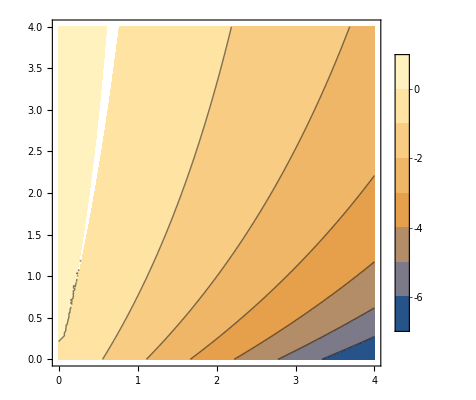

```mathematica
Show[ContourPlot[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,4},{ββ0,0,4},PlotLegends->Automatic]]
```

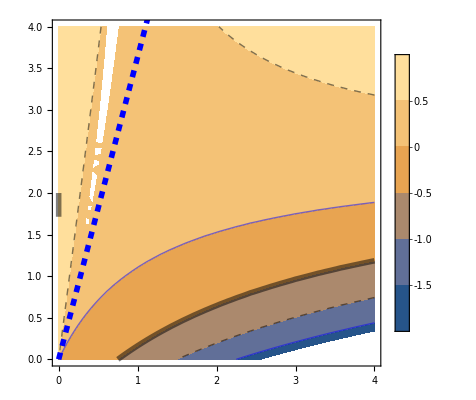

```mathematica
Show[ContourPlot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,4},{ββ0,0,4},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic],ContourPlot[ββ0==(δδ0+δδ0*(1-rr))/((1-cc)*(1-ϵϵ)),{δδ0,0,5},{ββ0,0,5},ContourStyle->{Thickness[0.01],Blue,Dashed}]]
```

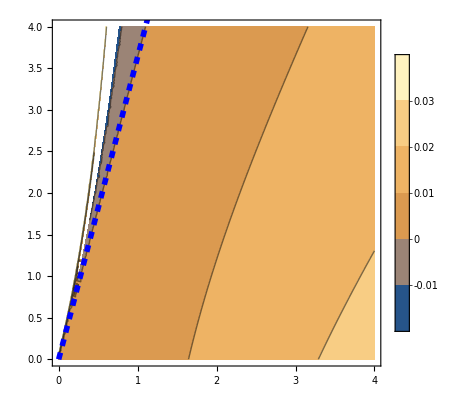

```mathematica
Show[ContourPlot[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,4},{ββ0,0,4},PlotLegends->Automatic],ContourPlot[ββ0==(δδ0+δδ0*(1-rr))/((1-cc)*(1-ϵϵ)),{δδ0,0,5},{ββ0,0,5},ContourStyle->{Thickness[0.01],Blue,Dashed}]]
```

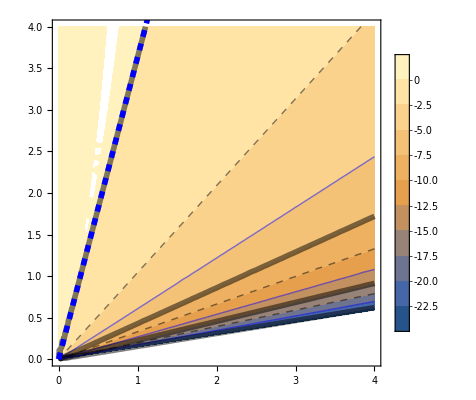

```mathematica
Show[ContourPlot[SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,4},{ββ0,0,4},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic],ContourPlot[ββ0==(δδ0+δδ0*(1-rr))/((1-cc)*(1-ϵϵ)),{δδ0,0,5},{ββ0,0,5},ContourStyle->{Thickness[0.01],Blue,Dashed}]]
```

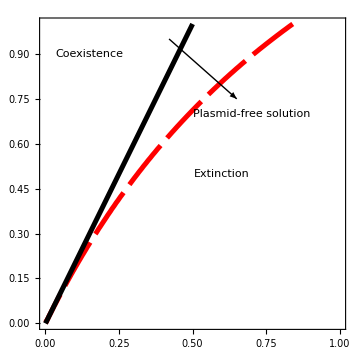

```mathematica
Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red,Dashing[{0.1,0.02}]}],ContourPlot[ββ0==(δδ0+δδ0),{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black},PlotLegends->Automatic],Graphics[Text[Style["Extinction"],{0.6,0.5}]],Graphics[Arrow[{{0.42,0.95},{0.65,0.75}}]],Graphics[Text[Style["Plasmid-free solution"],{0.7,0.7}]],Graphics[Text[Style["Coexistence"],{0.15,0.9}]],ImageSize->Medium,Frame->True,BaseStyle->texStyle,FrameLabel->MaTeX@{"\\delta_0","\\beta_0"}]
```

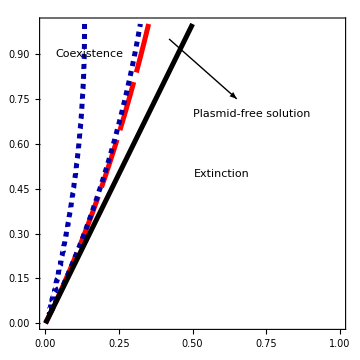

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;
δδc=0.05;
Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red,Dashing[{0.1,0.02}]}],ContourPlot[DiscriminantEigenvalues[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue],Dashing[0.01,0.02]}],ContourPlot[ββ0==(δδ0+δδ0),{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black},PlotLegends->Automatic],Graphics[Text[Style["Extinction"],{0.6,0.5}]],Graphics[Arrow[{{0.42,0.95},{0.65,0.75}}]],Graphics[Text[Style["Plasmid-free solution"],{0.7,0.7}]],Graphics[Text[Style["Coexistence"],{0.15,0.9}]],ImageSize->Medium,Frame->True,BaseStyle->texStyle,FrameLabel->MaTeX@{"\\delta_0","\\beta_0"}]
```

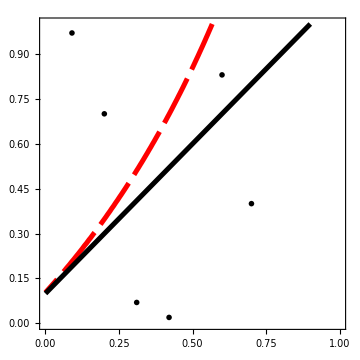

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;
δδc=0.05;δδ1=0.1;
Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ1,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Red,Dashing[{0.1,0.02}]}],ContourPlot[ββ0==(δδ0+δδ1),{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black},PlotLegends->Automatic],Graphics[Text[Style[MaTeX@"\\text{Extinction}"],{0.7,0.4}]],Graphics[Text[Style[MaTeX@"\\text{PFS}"],{0.6,0.83}]],Graphics[Text[Style[MaTeX@"\\boxed{\\gamma>\\delta_c}"],{0.09,0.97}]],Graphics[Text[Style[MaTeX@"\\text{Coexistence}"],{0.2,0.7}]],Graphics[Text[Style[MaTeX["\\gamma\\equiv\\text{effective conjugation rate}",FontSize->12]],{0.31,0.07}]],Graphics[Text[Style[MaTeX["\\delta_c\\equiv\\text{competition-induced mortality rate}",FontSize->12]],{0.42,0.02}]],ImageSize->Medium,Frame->True,BaseStyle->texStyle,FrameLabel->MaTeX@{"\\delta_0 \, \\text{(basal mortality)}","\\beta_0 \, \\text{(cell division rate)}"}]
```

```mathematica
1-(0.1+0.4)/0.53
```

0.0566038

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;δδ00=0.4;
δδc=0.05;δδ1=0.1;
res=Table[SteadySols[ββ00,ββ00*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],{ββ00,0,1,0.01}]
```

{{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.}},{{x0→0.,x1→0.},{x0→0.,x1→0.}},{{x0→0.0196078,x1→0.},{x0→0.,x1→0.}},{{x0→0.0384615,x1→0.},{x0→0.,x1→0.}},{{x0→0.0566038,x1→0.},{x0→0.,x1→0.}},{{x0→0.0740741,x1→0.},{x0→0.,x1→0.}},{{x0→0.0909091,x1→0.},{x0→0.,x1→0.}},{{x0→0.107143,x1→0.},{x0→0.,x1→0.}},{{x0→0.122807,x1→0.},{x0→0.,x1→0.}},{{x0→0.137931,x1→0.},{x0→0.,x1→0.}},{{x0→0.152542,x1→0.},{x0→0.,x1→0.}},{{x0→0.166667,x1→0.},{x0→0.,x1→0.}},{{x0→0.180328,x1→0.},{x0→0.,x1→0.}},{{x0→0.193548,x1→0.},{x0→0.,x1→0.}},{{x0→0.206349,x1→0.},{x0→0.,x1→0.}},{{x0→0.21875,x1→0.},{x0→0.,x1→0.}},{{x0→0.230769,x1→0.},{x0→0.,x1→0.}},{{x0→0.242424,x1→0.},{x0→0.,x1→0.}},{{x0→0.253731,x1→0.},{x0→0.242313,x1→0.004475},{x0→0.,x1→0.}},{{x0→0.264706,x1→0.},{x0→0.239294,x1→0.0100504},{x0→0.,x1→0.}},{{x0→0.275362,x1→0.},{x0→0.236296,x1→0.0155895},{x0→0.,x1→0.}},{{x0→0.285714,x1→0.},{x0→0.23332,x1→0.0210926},{x0→0.,x1→0.}},{{x0→0.295775,x1→0.},{x0→0.230364,x1→0.02656},{x0→0.,x1→0.}},{{x0→0.305556,x1→0.},{x0→0.227429,x1→0.0319921},{x0→0.,x1→0.}},{{x0→0.315068,x1→0.},{x0→0.224515,x1→0.0373893},{x0→0.,x1→0.}},{{x0→0.324324,x1→0.},{x0→0.221621,x1→0.0427518},{x0→0.,x1→0.}},{{x0→0.333333,x1→0.},{x0→0.218747,x1→0.0480801},{x0→0.,x1→0.}},{{x0→0.342105,x1→0.},{x0→0.215893,x1→0.0533744},{x0→0.,x1→0.}},{{x0→0.350649,x1→0.},{x0→0.213059,x1→0.0586352},{x0→0.,x1→0.}},{{x0→0.358974,x1→0.},{x0→0.210245,x1→0.0638626},{x0→0.,x1→0.}},{{x0→0.367089,x1→0.},{x0→0.207451,x1→0.0690571},{x0→0.,x1→0.}},{{x0→0.375,x1→0.},{x0→0.204676,x1→0.0742189},{x0→0.,x1→0.}},{{x0→0.382716,x1→0.},{x0→0.201921,x1→0.0793483},{x0→0.,x1→0.}},{{x0→0.390244,x1→0.},{x0→0.199185,x1→0.0844457},{x0→0.,x1→0.}},{{x0→0.39759,x1→0.},{x0→0.196468,x1→0.0895114},{x0→0.,x1→0.}},{{x0→0.404762,x1→0.},{x0→0.19377,x1→0.0945457},{x0→0.,x1→0.}},{{x0→0.411765,x1→0.},{x0→0.191091,x1→0.0995488},{x0→0.,x1→0.}},{{x0→0.418605,x1→0.},{x0→0.188432,x1→0.104521},{x0→0.,x1→0.}},{{x0→0.425287,x1→0.},{x0→0.18579,x1→0.109463},{x0→0.,x1→0.}},{{x0→0.431818,x1→0.},{x0→0.183168,x1→0.114374},{x0→0.,x1→0.}},{{x0→0.438202,x1→0.},{x0→0.180564,x1→0.119256},{x0→0.,x1→0.}},{{x0→0.444444,x1→0.},{x0→0.177978,x1→0.124108},{x0→0.,x1→0.}},{{x0→0.450549,x1→0.},{x0→0.175411,x1→0.12893},{x0→0.,x1→0.}},{{x0→0.456522,x1→0.},{x0→0.172862,x1→0.133723},{x0→0.,x1→0.}},{{x0→0.462366,x1→0.},{x0→0.170331,x1→0.138487},{x0→0.,x1→0.}},{{x0→0.468085,x1→0.},{x0→0.167819,x1→0.143223},{x0→0.,x1→0.}},{{x0→0.473684,x1→0.},{x0→0.165324,x1→0.14793},{x0→0.,x1→0.}},{{x0→0.479167,x1→0.},{x0→0.162848,x1→0.15261},{x0→0.,x1→0.}},{{x0→0.484536,x1→0.},{x0→0.160389,x1→0.157261},{x0→0.,x1→0.}},{{x0→0.489796,x1→0.},{x0→0.157949,x1→0.161885},{x0→0.,x1→0.}},{{x0→0.494949,x1→0.},{x0→0.155526,x1→0.166481},{x0→0.,x1→0.}},{{x0→0.5,x1→0.},{x0→0.153121,x1→0.171051},{x0→0.,x1→0.}}}

```mathematica
Ext1x0 = Table[{(i-1)*0.01,x0}/.Last[res[[i]]],{i,1,Length[res]}];
```

```mathematica
Ext1x1 = Table[{(i-1)*0.01,x1}/.Last[res[[i]]],{i,1,Length[res]}];
```

```mathematica
PFS1x0 = Table[If[Length[res[[i]]]==3,{(i-1)*0.01,x0}/.res[[i]][[2]],If[Length[res[[i]]]==2,{(i-1)*0.01,x0}/.res[[i]][[1]],{(i-1)*0.01,-100}]],{i,1,Length[res]}];
```

```mathematica
PFS1x1 = Table[If[Length[res[[i]]]==3,{(i-1)*0.01,x1}/.res[[i]][[2]],If[Length[res[[i]]]==2,{(i-1)*0.01,x1}/.res[[i]][[1]],{(i-1)*0.01,-100}]],{i,1,Length[res]}];
```

```mathematica
C1x0 = Table[If[Length[res[[i]]]==3,{(i-1)*0.01,x0}/.res[[i]][[1]],{(i-1)*0.01,-100}],{i,1,Length[res]}];
```

```mathematica
C1x1 = Table[If[Length[res[[i]]]==3,{(i-1)*0.01,x1}/.res[[i]][[1]],{(i-1)*0.01,-100}],{i,1,Length[res]}];
```

```mathematica
δδ00=0.17
```

0.17

```mathematica
δδ00+δδ1
```

0.27

```mathematica
,Plot[{Solx0PFS[ββ0,δδ00,δδ1],SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc]},{ββ0,0.,1},PlotRange->{0,0.6},Frame->True,PlotStyle->{{Thick,Red},{Thick,Black}}],Plot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],{ββ0,0.31,1},PlotStyle->{{Thick,Black,Dashing[0.01,0.02]}}],
```

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;δδ00=0.17;
δδc=0.05;δδ1=0.1;
```

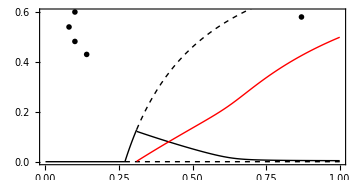

```mathematica
P1=Show[Plot[0,{ββ0,0,δδ00+δδ1},PlotStyle->{Thick,Black},Frame->True],Plot[0,{ββ0,δδ00+δδ1,1},PlotStyle->{Thick,Black,Dashing[0.01,0.02]}],Plot[{Solx0PFS[ββ0,δδ00,δδ1]},{ββ0,δδ00+δδ1,0.31},PlotRange->{0,1},Frame->True,PlotStyle->{Thick,Black}],Plot[{Solx0PFS[ββ0,δδ00,δδ1],SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc]},{ββ0,0.31,1},Frame->True,PlotStyle->{{Thick,Black,Dashing[0.01,0.02]},{Thick,Black}}],Plot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],{ββ0,0.31,1},PlotStyle->{{Thick,Red}}],Graphics[Text[Style[MaTeX["x_0^{*}: \\text{black}",FontSize->12]],{0.1,0.6}]],Graphics[Text[Style[MaTeX["x_1^{*}: \\text{red}",FontSize->12]],{0.08,0.54}]],Graphics[Text[Style[MaTeX["\\text{stable: }-",FontSize->12]],{0.1,0.482}]],Graphics[Text[Style[MaTeX["\\text{unstable: }\\cdots",FontSize->12]],{0.14,0.43}]],Graphics[Text[Style[MaTeX["\\boxed{\\gamma>\\delta_c=0.17}",FontSize->10]],{0.87,0.58}]],ImageSize->Medium,Frame->True,BaseStyle->texStyle,PlotRange->{{0,1},{0,0.6}},AspectRatio->0.5]
```

```mathematica
FrameLabel->{MaTeX["\\beta_0 \, \\text{(cell division rate)}",FontSize->16],MaTeX[ "x_0^{*},\, x_1^{*}\, (\\text{plasmid, bacteria})",FontSize->12]}
```

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;δδ1=0.1;
δδc=3;
```

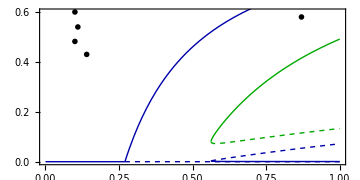

```mathematica
P2=Show[Plot[0,{ββ0,0,δδ00+δδ1},PlotStyle->{Thick,Darker[Blue]},Frame->True],Plot[0,{ββ0,δδ00+δδ1,1},PlotStyle->{Thick,Darker[Blue],Dashing[0.01,0.02]}],Plot[{Solx0PFS[ββ0,δδ00,δδ1]},{ββ0,δδ00+δδ1,1},PlotRange->{0,1},Frame->True,PlotStyle->{Thick,Darker[Blue]}],Plot[{SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc]},{ββ0,0.56,1},PlotRange->{0,1},Frame->True,PlotStyle->{{Thick,Darker[Blue]}}],Plot[{SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc]},{ββ0,0.56,1},PlotRange->{0,1},Frame->True,PlotStyle->{{Thick,Darker[Blue],Dashing[0.01,0.02]}}],Plot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],{ββ0,0.56,1},PlotStyle->{{Thick,Darker[Green]}}],Plot[SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],{ββ0,0.56,1},PlotStyle->{{Thick,Darker[Green],Dashing[0.01,0.02]}}],Graphics[Text[Style[MaTeX["x_0^{*}: \\text{blue}",FontSize->12]],{0.1,0.6}]],Graphics[Text[Style[MaTeX["x_1^{*}: \\text{green}",FontSize->12]],{0.11,0.54}]],Graphics[Text[Style[MaTeX["\\text{stable: }-",FontSize->12]],{0.1,0.482}]],Graphics[Text[Style[MaTeX["\\text{unstable: }\\cdots",FontSize->12]],{0.14,0.43}]],Graphics[Text[Style[MaTeX["\\boxed{\\gamma<\\delta_c=0.17}",FontSize->10]],{0.87,0.58}]],ImageSize->Medium,Frame->True,BaseStyle->texStyle,PlotRange->{{0,1},{0,0.6}},AspectRatio->0.5]
```

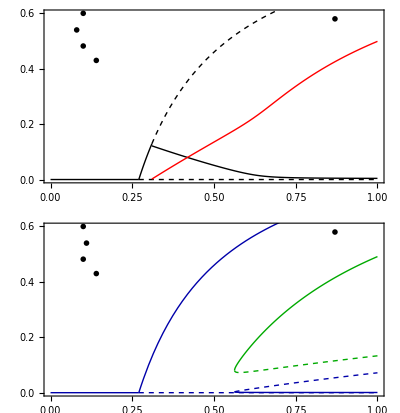

```mathematica
GraphicsGrid[{{P1},{P2}},AspectRatio->Full,AxesLabel->{MaTeX["\\beta_0 \, \\text{(cell division rate)}",FontSize->16],MaTeX[ "x_0^{*},\, x_1^{*}\, (\\text{plasmid, bacteria})",FontSize->12]}]
```

```mathematica
δδ00+δδ1B
```

0.27

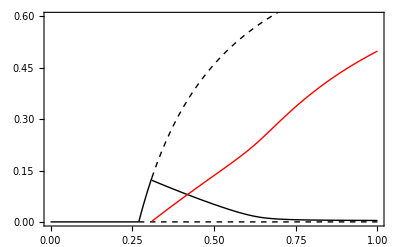

```mathematica
Show[Plot[0,{ββ0,0,δδ00+δδ1},PlotStyle->{Thick,Black},Frame->True],Plot[0,{ββ0,δδ00+δδ1,1},PlotStyle->{Thick,Black,Dashing[0.01,0.02]}],Plot[{Solx0PFS[ββ0,δδ00,δδ1]},{ββ0,δδ00+δδ1,0.31},PlotRange->{0,1},Frame->True,PlotStyle->{Thick,Black}],Plot[{Solx0PFS[ββ0,δδ00,δδ1],SolDoublex0A[ββ0,ββ0*(1-ccB),ϵϵB,γγB,δδ00,δδ1,δδ1*(1-rrB),δδcB]},{ββ0,0.31,1},Frame->True,PlotStyle->{{Thick,Black,Dashing[0.01,0.02]},{Thick,Black}}],Plot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-ccB),ϵϵB,γγB,δδ00,δδ1,δδ1*(1-rrB),δδcB],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rrB),δδcB],{ββ0,0.31,1},PlotStyle->{{Thick,Red}}],PlotRange->{{0,1},{0,0.6}}]
```

```mathematica
rrB=0.2;ϵϵB=0.01;ccB=0.5;γγB=1;
δδcB=0.05;δδ1B=0.1;
```

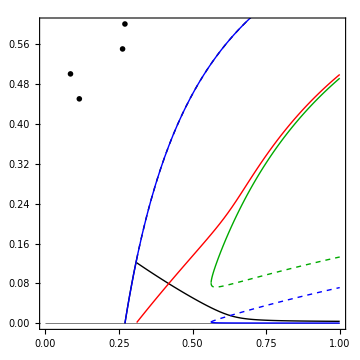

```mathematica
Show[Plot[0,{ββ0,0,δδ00+δδ1},PlotStyle->{Thick,White},Frame->True],Plot[0,{ββ0,0,1},PlotStyle->{Thickness[0.001],Black}],Plot[{Solx0PFS[ββ0,δδ00,δδ1]},{ββ0,δδ00+δδ1,0.31},PlotRange->{0,1},Frame->True,PlotStyle->{Thick,Black}],Plot[{Solx0PFS[ββ0,δδ00,δδ1],SolDoublex0A[ββ0,ββ0*(1-ccB),ϵϵB,γγB,δδ00,δδ1,δδ1*(1-rrB),δδcB]},{ββ0,0.31,1},Frame->True,PlotStyle->{{Thick,Black,Dashing[0.01,0.02]},{Thick,Black}}],Plot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-ccB),ϵϵB,γγB,δδ00,δδ1,δδ1*(1-rrB),δδcB],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rrB),δδcB],{ββ0,0.31,1},PlotStyle->{{Thick,Red}}],Plot[{Solx0PFS[ββ0,δδ00,δδ1]},{ββ0,δδ00+δδ1,1},PlotRange->{0,1},Frame->True,PlotStyle->{Thick,Blue}],Plot[{SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc]},{ββ0,0.56,1},PlotRange->{0,1},Frame->True,PlotStyle->{{Thick,Blue}}],Plot[{SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc]},{ββ0,0.56,1},PlotRange->{0,1},Frame->True,PlotStyle->{{Thick,Blue,Dashing[0.01,0.02]}}],Plot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],{ββ0,0.56,1},PlotStyle->{{Thick,Darker[Green]}}],Plot[SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],{ββ0,0.56,1},PlotStyle->{{Thick,Darker[Green],Dashing[0.01,0.02]}}],Graphics[Text[Style[MaTeX["x_0^{*}: \\text{blue}(\\gamma<\\delta_c),\, \\text{black}(\\gamma>\\delta_c)",FontSize->10]],{0.27,0.6}]],Graphics[Text[Style[MaTeX["x_1^{*}: \\text{green}(\\gamma<\\delta_c),\, \\text{red}(\\gamma>\\delta_c)",FontSize->10]],{0.262,0.55}]],Graphics[Text[Style[MaTeX["\\text{stable: }-",FontSize->10]],{0.085,0.5}]],Graphics[Text[Style[MaTeX["\\text{unstable: }\\cdots",FontSize->10]],{0.115,0.45}]],ImageSize->Medium,Frame->True,BaseStyle->texStyle,FrameLabel->MaTeX@{"\\beta_0 \, \\text{(cell division rate)}", "x_0^{*},\, x_1^{*}\, (\\text{plasmid, bacteria})"},PlotRange->{{0,1},{0,0.6}},AspectRatio->1]
```

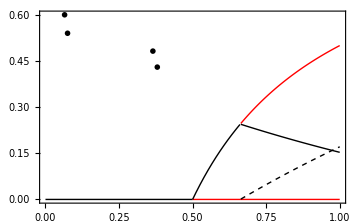

```mathematica
Show[Plot[0,{ββ0,0,δδ00+δδ1},PlotStyle->{Thick,Black},Frame->True],Plot[0,{ββ0,δδ00+δδ1,1},PlotStyle->{Thick,Red}],Plot[{Solx0PFS[ββ0,δδ00,δδ1]},{ββ0,0,0.661},PlotRange->{0,0.6},Frame->True,PlotStyle->{Thick,Black}],Plot[{Solx0PFS[ββ0,δδ00,δδ1],SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc]},{ββ0,0.664,1},PlotRange->{0,0.6},Frame->True,PlotStyle->{{Thick,Red},{Thick,Black}}],Plot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ00,δδ1,δδ1*(1-rr),δδc],{ββ0,0.664,1},PlotStyle->{{Thick,Black,Dashing[0.01,0.02]}}],Graphics[Text[Style[MaTeX["x_0^{*}: -",FontSize->12]],{0.065,0.6}]],Graphics[Text[Style[MaTeX["x_1^{*}: \\cdots",FontSize->12]],{0.075,0.54}]],Graphics[Text[Style[MaTeX["\\text{stable: black}(\\gamma>\\delta_c)\\text{, blue}(\\gamma<\\delta_c)",FontSize->12]],{0.365,0.482}]],Graphics[Text[Style[MaTeX["\\text{unstable: red}(\\gamma>\\delta_c)\\text{, green}(\\gamma<\\delta_c)",FontSize->12]],{0.38,0.43}]],ImageSize->Medium,Frame->True,BaseStyle->texStyle,FrameLabel->MaTeX@{"\\beta_0 \, \\text{(cell division rate)}", "x_0^{*},\, x_1^{*}\, (\\text{plasmid, bacteria})"},PlotRange->{{0,1},{0,0.6}}]
```

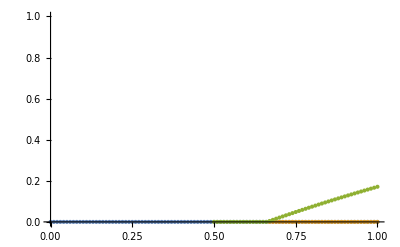

```mathematica
ListPlot[{Ext1x1,C1x1,PFS1x1},PlotRange->{0,1}]
```

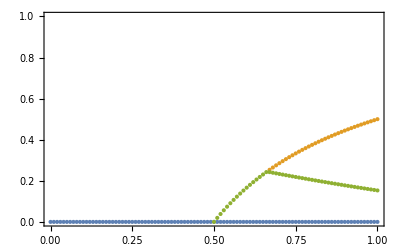

```mathematica
ListPlot[{Ext1x0,C1x0,PFS1x0},Frame->True,PlotRange->{0,1}]
```

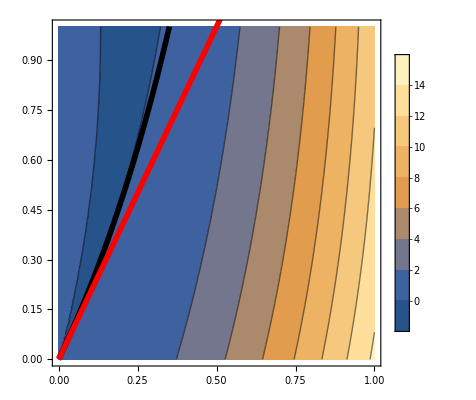

```mathematica
Show[ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[DiscriminantEigenvalues[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Black}],ContourPlot[ββ0==δδ0+δδ0,{δδ0,0,10},{ββ0,0,10},ContourStyle->{Thickness[0.01],Red}]]
```

```mathematica
λ2[ββ0,ϵϵ,γγ,δδ0,δδ0,δδc,cc,rr]
```

0.935567

```mathematica
ββ0
```

2.653

```mathematica
δδ0
```

0.3387

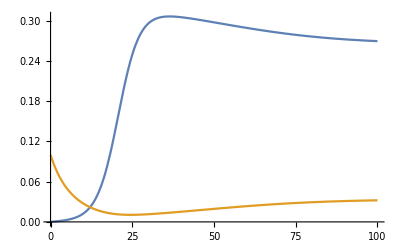

```mathematica
ββ0=1;δδ0=0.3328;ϵϵ=0.01;Plot[{x0[t]/.Sols[0.,0.1,ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],x1[t]/.Sols[0.,0.1,ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]},{t,0,100}]
```

```mathematica
_
```

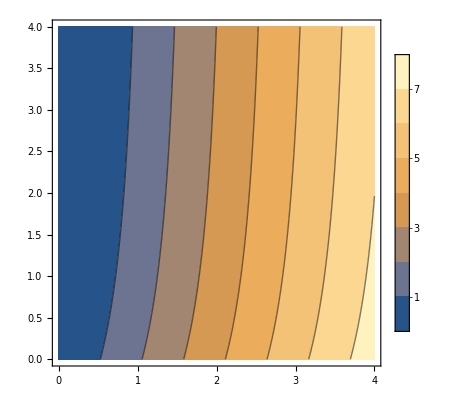

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;
δδc=0.05;Show[ContourPlot[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,4},{ββ0,0,4},PlotLegends->Automatic]]
```

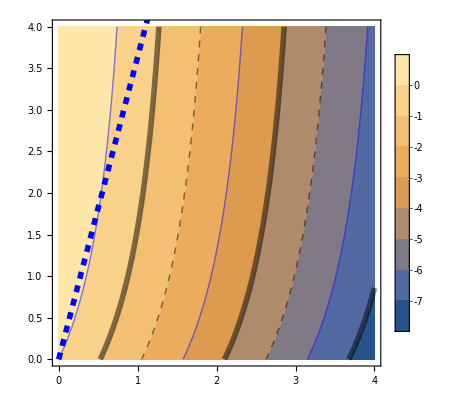

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;
δδc=0.05;Show[ContourPlot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,4},{ββ0,0,4},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic],ContourPlot[ββ0==(δδ0+δδ0*(1-rr))/((1-cc)*(1-ϵϵ)),{δδ0,0,5},{ββ0,0,5},ContourStyle->{Thickness[0.01],Blue,Dashed}]]
```

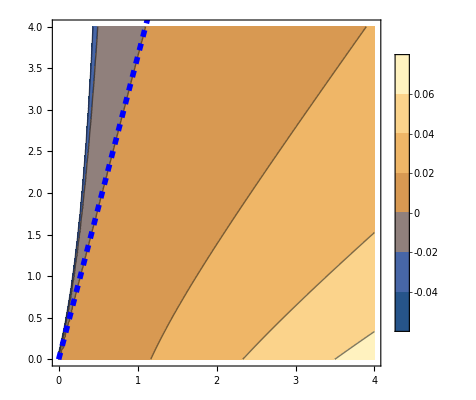

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;
δδc=0.05;Show[ContourPlot[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,4},{ββ0,0,4},PlotLegends->Automatic],ContourPlot[ββ0==(δδ0+δδ0*(1-rr))/((1-cc)*(1-ϵϵ)),{δδ0,0,5},{ββ0,0,5},ContourStyle->{Thickness[0.01],Blue,Dashed}]]
```

```mathematica
SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]
```

-0.000174503

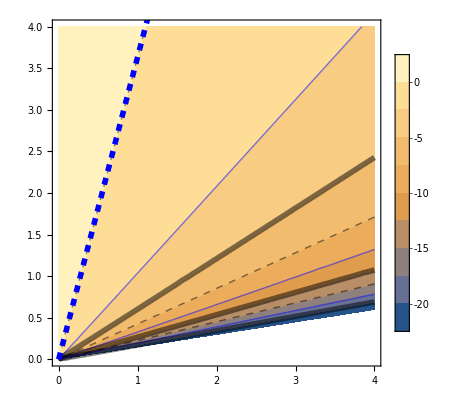

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;
δδc=0.05;Show[ContourPlot[SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],{δδ0,0,4},{ββ0,0,4},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic],ContourPlot[ββ0==(δδ0+δδ0*(1-rr))/((1-cc)*(1-ϵϵ)),{δδ0,0,5},{ββ0,0,5},ContourStyle->{Thickness[0.01],Blue,Dashed}]]
```

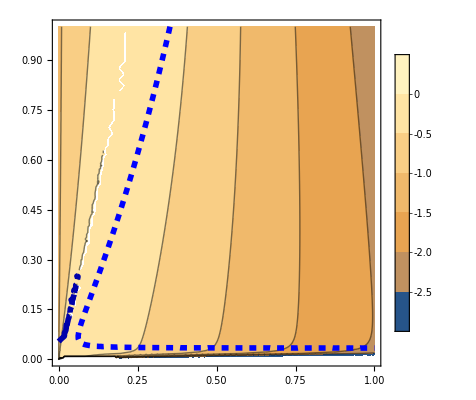

```mathematica
rr=0.2;ϵϵ=0.01;cc=0.5;γγ=1;
δδc=0.05;Show[ContourPlot[Re[Eigenvalues[JacDynamics2[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]][[1]]],{δδ0,0,1},{ββ0,0,1},PlotLegends->Automatic],ContourPlot[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Darker[Blue]}],ContourPlot[SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]==0,{δδ0,0,1},{ββ0,0,1},ContourStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Automatic]]
```

```mathematica
δδ0=0.428;ββ0=4.883;Eigenvalues[JacDynamics2[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],SolDoublex1[SolDoublex0A[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]]
```

{-1.60709-0.13196 ⅈ,-0.0230657-0.166025 ⅈ}

```mathematica
δδ0=0.428;ββ0=4.883;Eigenvalues[JacDynamics2[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]]
```

{-1.60709+0.13196 ⅈ,-0.0230657+0.166025 ⅈ}

```mathematica
δδ0=0.3387;ββ0=2.653;Eigenvalues[JacDynamics2[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],SolDoublex1[SolDoublex0B[ββ0,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc],ββ0,0.,ββ0*(1-cc),ϵϵ,γγ,δδ0,δδ0,δδ0*(1-rr),δδc]]
```

{-0.6915+0.0271499 ⅈ,-0.00924947+0.148244 ⅈ}